# Steam-Punk Lambda: General Computation with 4x4 Matrices

## Brian Beckman, Erik Meijer, David Leibs Dec 2012 Brisbane, Australia

Can we do arbitrary computations using only operations on 4x4 matrices? We'd like that since we might be able to run them on a GPU. The idea is to compile ordinary code to operations on 4x4 matrices, as if that were the instruction set of our machine. Contrast this against OpenACC or CUDA, which are basically DSLs for the GPU embedded in ordinary programming languages. Those give you ways to write "machine-sympathetic code" for the GPU in C or C++ or whatever.

## EVERYTHING IS A 4X4 MATRIX

### Symbolic matrices

```mathematica
script[c_]:=Quiet@ToExpression["\\[Script"<>"Capital"<>ToUpperCase[ToString[c]]<>"]"]
```

```mathematica
double[c_]:=Quiet@ToExpression["\\[DoubleStruck"<>"Capital"<>ToUpperCase[ToString[c]]<>"]"]
```

```mathematica
greek[c_]:=Quiet@ToExpression[ToString[c]/.{"a"->α,"b"->β,"c"->γ,"d"->δ,"e"->ϵ,"f"->ϕ,"g"->χ,"h"->η,"i"->ι,"j"->φ,"k"->κ,"l"->λ,"m"->μ,"n"->ν,"o"->ο,"p"->π,"q"->θ,"r"->ρ,"s"->σ,"t"->τ,"u"->υ,"w"->ω,"x"->ξ,"y"->ψ,"z"->ζ}]
```

```mathematica
pv[ul_,ur_,ll_,lr_]:=({{ul, ur, greek@ul, greek@ur}, {ll, lr, greek@ll, greek@lr}, {script@ul, script@ur, double@ul, double@ur}, {script@ll, script@lr, double@ll, double@lr}})
```

### Standard display ideas from the "Insert" menu

Consider arbitrary 4x4 matrices, broken into four 2x2 blocks.

```mathematica
Grid@{MatrixForm/@
{p=pv[a,b,c,d],
q=pv[x,y,z,w]}}
```

(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)

### New display ideas from the @SE chat room

Thanks to Rojo @Mathematica.stackexchange.com for this idea... something to develop

```mathematica
Grid[p,Dividers->{{{True,False}},{{True,False}}}]
```

a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻

Thanks to rm-rf @Mathematica.stackexchange.com for this

```mathematica
Grid[(MatrixForm/@Transpose@Partition[#,2])&/@Fold[Partition[#1,#2]&,Flatten@p,{2,4}],Frame->All]
```

(a | b
c | d) | (α | β
γ | δ)
(𝒜 | ℬ
𝒞 | 𝒟) | (𝔸 | 𝔹
ℂ | 𝔻)

Thanks to rojo @Mathematica.stackexchange.com

```mathematica
Grid[Map[MatrixForm,Partition[p,{2,2}],{2}],Frame->All]
```

(a | b
c | d) | (α | β
γ | δ)
(𝒜 | ℬ
𝒞 | 𝒟) | (𝔸 | 𝔹
ℂ | 𝔻)

### The upper-left corner is special

Divide matrices into equivalence classes:

All matrices with the same upper-left 2x2 block are equivalent -- they all represent the same value in the system. The contents of the other three blocks are "machine-state," but the value of the matrix as a whole is just the value of the 2x2 block in the upper-left corner.

The prime representative of an equivalence class is the [CHIEF] of that class. It has the same upper-left 2x2 as every other member of the class, but zeros elsewhere. To test whether two matrices are equivalent, compare them both to their chiefs.

The [MACHINE-STATE] of a matrix is the contents of all the blocks other than the upper-left 2x2 block.

## PRIMITIVE MATRICES

```mathematica
ill=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});iul=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});iur=({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});ilr=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
inf=({{Infinity, 0, 0, 0}, {0, Infinity, 0, 0}, {0, 0, Infinity, 0}, {0, 0, 0, Infinity}});
```

Convenience:

```mathematica
ClearAll[T,M];
T=Transpose;M=MatrixForm;
```

Investigate what any particular operator does to a sample matrix in various combinations, namely m.p.m^T, m^T.p.m, and so on:

```mathematica
combos[m_,p_]:=With[{mT=m//T},
Grid[{
M/@{m.p,p.mT,m.p.mT},
M/@{mT.p,p.m,mT.p.m}
}]];
combos[ill,p]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
a | b | α | β
c | d | γ | δ) | (0 | 0 | a | b
0 | 0 | c | d
0 | 0 | 𝒜 | ℬ
0 | 0 | 𝒞 | 𝒟) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d)
(𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (α | β | 0 | 0
γ | δ | 0 | 0
𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0) | (𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
combos[iul,p]
```

(a | b | α | β
c | d | γ | δ
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | 0 | 0
c | d | 0 | 0
𝒜 | ℬ | 0 | 0
𝒞 | 𝒟 | 0 | 0) | (a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(a | b | α | β
c | d | γ | δ
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | 0 | 0
c | d | 0 | 0
𝒜 | ℬ | 0 | 0
𝒞 | 𝒟 | 0 | 0) | (a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## REGISTERS

Think of a 4x4 matrix as a machine with four registers: ul, ur, ll, lr, for "upper-left," "upper-right," "lower-left," and "lower-right."

```mathematica
registers={iul,iur,ill,ilr};
```

ul is like EAX in the x86 machine: it's a special register where you can find the result of a computation and where you expect the value of an actual argument to a unary function to appear.

## INSTRUCTIONS

### The MV Instruction

I can move the CHIEF in the upper left corner into any one of the four registers.

```mathematica
MV[reg_,m_]:=reg/.{
iul->iul.m.(iul//T),
iur->iul.m.(ill//T),
ill->ill.m.(iul//T),
ilr->ill.m.(ill//T)
}
```

```mathematica
Grid[{(MV[#,p]//M)&/@registers}]
```

(a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | a | b
0 | 0 | c | d
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
a | b | 0 | 0
c | d | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d)

MV is hippocratic: If its first argument is not a register, MV produces its first argument.

```mathematica
MV[p,q]//M
```

(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

### The AMV Instruction

Move any one of the four registers into ul, the CHIEF position. These operations are all conjugates of the corresponding MV instructions.

```mathematica
AMV[reg_,m_]:=reg/.{
iul->iul.m.(iul//T),
iur->(iul//T).m.ill,
ill->(ill//T).m.iul,
ilr->(ill//T).m.ill
}
```

```mathematica
Grid[{(AMV[#,p]//M)&/@registers}]
```

(a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (α | β | 0 | 0
γ | δ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (𝒜 | ℬ | 0 | 0
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### The CHF Instruction

Extract the CHIEF of any matrix by masking off the MACHINE-STATE portion

```mathematica
CHF[m_]:=iul.m.(iul//T);
```

```mathematica
CHF[p]//M
```

(a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### The ST Instruction

Extract the MACHINE-STATE from any matrix -- the ANTI-CHIEF as it were.

```mathematica
ST[m_]:=m-CHF[m]
```

```mathematica
ST[p]//M
```

(0 | 0 | α | β
0 | 0 | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
Grid[{M/@{ap=ST[p],aq=ST[q]}}]
```

(0 | 0 | α | β
0 | 0 | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | ξ | ψ
0 | 0 | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)

### The CY instruction

```mathematica
CY[r1_,r2_,m_]:=MV[r2,AMV[r1,m]]
```

```mathematica
Grid@{M/@{CY[iul,ilr,p],CY[ilr,iul,p]}}
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d) | (𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Grid@(Outer[M@CY[#1,#2,p]&,registers,registers,1])
```

(a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | a | b
0 | 0 | c | d
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
a | b | 0 | 0
c | d | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d)
(α | β | 0 | 0
γ | δ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | α | β
0 | 0 | γ | δ
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
α | β | 0 | 0
γ | δ | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
0 | 0 | γ | δ)
(𝒜 | ℬ | 0 | 0
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 𝒜 | ℬ
0 | 0 | 𝒞 | 𝒟
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
𝒜 | ℬ | 0 | 0
𝒞 | 𝒟 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝒜 | ℬ
0 | 0 | 𝒞 | 𝒟)
(𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 𝔸 | 𝔹
0 | 0 | ℂ | 𝔻
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝔸 | 𝔹
0 | 0 | ℂ | 𝔻)

### Booleans

```mathematica
falseMatrix=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});trueMatrix=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

trueMatrix composed with any matrix is that matrix

```mathematica
trueMatrix.p===p
```

True

falseMatrix annihilates any matrix

```mathematica
falseMatrix.p===falseMatrix
```

True

A falsey matrix is one whose CHIEF matches the false matrix

```mathematica
falsey[m_]:=CHF[m]===falseMatrix
```

A truthy matrix is one whose CHIEF is not falsey

```mathematica
truthy[m_]:=CHF[m]=!=falseMatrix
```

The other registers don't matter when testing truthiness or falseyness

```mathematica
(truthy[MV[#,p]])&/@registers
```

{True,False,False,False}

```mathematica
(falsey[MV[#,p]])&/@registers
```

{False,True,True,True}

## GENETIC SEARCH FOR NAND

First, write a postfix calculator for instructions so that we can construct strings of instructions. Then, treat those strings as genomes and genetically search for the fomulas we need (David says: maybe we can use probabilistic fitness functions)

### Stack

```mathematica
ClearAll[pushR,popR,dupR,rotR,swapR,topR,nextR,thirdR];
(* stack-to-stack transforms *)
pushR={{{stack___},datum_}:>{datum,stack}};
popR={{top_,rest___}:>{rest}};
dupR={{top_,rest___}:>{top,top,rest}};
rotR={{top_,rest___}:>{rest,top}};
swapR={{top_,next_,rest___}:>{next,top,rest}};
(* stack-to-value transforms *)
topR={{top_,___}:>top,{}:>falseMatrix};
nextR={{top_,next_,___}:>next,({_}|{}):>falseMatrix};
thirdR={{top_,next_,third_,___}:>third,({_}|{a_,b_}|{}):>falseMatrix};
```

### Exec

MV, AMV, and CY are unsuitable for machine instructions because they have an implicit if-test in them. We need to construct if-tests from more primitive operations: plus, dot, minus, inverse, conjugation, determinant, trace, transpose, commutator, etc.

```mathematica
ClearAll[instructionSet];
instructionSet=
{(*MV,AMV,CY,*)nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,uminus,inv,det,tr,
T,CHF,ST,
dup,swap,rot,pop,(*nop,*)true,false,ul,ur,ll,lr};
ClearAll[exec,execTrace,execAll,execAllTrace,gridStack,microcode,myInv];
ClearAll/@
{(*MV,AMV,CY,*)nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,inv,uminus,det,tr,
(*T,CHF,ST,*)
dup,swap,rot,pop,(*nop,*)true,false,ul,ur,ll,lr};
myInv[m_]:=Quiet@Check[Inverse[m],inf];
microcode=Dispatch@{
(* NOP -- for padding instruction strings *)
{stack_,nop}:>stack,
(* TERNARY *)
{stack_,conj2}:>
With[{
nT=T@(stack/.topR),
p=stack/.nextR,
m=stack/.thirdR},
{stack/.popR/.popR/.popR,m.p.nT}/.pushR],
{stack_,conj2I}:>
With[{
nI=myInv@(stack/.topR),
p=stack/.nextR,
m=stack/.thirdR},
{stack/.popR/.popR/.popR,m.p.nI}/.pushR],
(*CY,With[{r=CY[third,next,top]},pop[];pop[];pop[];push[r]],*)
(* BINARIES *)
(*MV,With[{r=MV[next,top]},pop[];pop[];push[r]],*)
(*AMV,With[{r=AMV[next,top]},pop[];pop[];push[r]],*)
{stack_,plus}:>
With[{r=(stack/.nextR)+(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,dot}:>
With[{r=(stack/.nextR).(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,minus}:>
With[{r=(stack/.nextR)-(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,div}:>
With[{r=(stack/.nextR).myInv[stack/.topR]},
{stack/.popR/.popR,r}/.pushR],
{stack_,conj}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(T@m)}/.pushR],
{stack_,conjI}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(myInv@m)}/.pushR],
{stack_,comm}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(T@m).(T@p)}/.pushR],
{stack_,commI}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(myInv@m).(myInv@p)}/.pushR],
(* UNARIES *)
{stack_,uminus}:>
({stack/.popR,(-trueMatrix.(stack/.topR))}/.pushR),
{stack_,inv}:>
({stack/.popR,myInv@(stack/.topR)}/.pushR),
{stack_,det}:>
({stack/.popR,trueMatrix*Det[stack/.topR]}/.pushR),
{stack_,tr}:>With[{r=stack/.topR},
{stack/.popR,trueMatrix*Plus@@Table[r⟦i,i⟧,{i,4}]}/.pushR],
{stack_,T}:>
({stack/.popR,T@(stack/.topR)}/.pushR),
{stack_,CHF}:>
({stack/.popR,CHF[stack/.topR]}/.pushR),
{stack_,ST}:>
({stack/.popR,r=ST[stack/.topR]}/.pushR),
(* NULLARIES *)
{stack_,dup}:>(stack/.dupR),
{stack_,swap}:>(stack/.swapR),
{stack_,rot}:>(stack/.rotR),
{stack_,pop}:>(stack/.popR),
(*nop,0,*)
(* CONSTANTS *)
{stack_,true}:>({stack,trueMatrix}/.pushR),
{stack_,false}:>({stack,falseMatrix}/.pushR),
{stack_,ul}:>({stack,iul}/.pushR),
{stack_,ur}:>({stack,iur}/.pushR),
{stack_,ll}:>({stack,ill}/.pushR),
{stack_,lr}:>({stack,ilr}/.pushR),
(* DEFAULT *)
{stack_,x_}:>({stack,x}/.pushR)
};
exec[stack_,instr_]:=Chop@({stack,instr}/.microcode);
exec[___]:=Throw["bad exec: "<>ToString@{___}];
execTrace[stack_,instr_]:=gridStack@Reverse@exec[stack,instr];
execAll[stack_,instrs_]:=gridStack@Fold[exec,stack,instrs];
execAllTrace[stack_,instrs_]:=With[{history=Grid[{#},Frame->All]&/@((M/@#)&/@Reverse/@FoldList[exec,stack,instrs])},Grid[Partition[Join[{start},Riffle[history,M/@instrs]],2],Frame->All]];gridStack[stack_]:=Grid[{M/@stack},Frame->All]
```

### Unit Tests

```mathematica
ClearAll[pstack,qstack,pqstack,ranstack];
pstack=({{},p}/.pushR);
qstack=({{},q}/.pushR);
pqstack={{{},p}/.pushR,q}/.pushR;
ranmat[]:=RandomReal[{0.,1.},{4,4}];
ranstack[n_:1]:=Fold[{#1,#2}/.pushR&,{},RandomReal[{0.,1.},{n,4,4}]]
```

#### conj2

```mathematica
M@(iul.p.(T@ill))
```

(0 | 0 | a | b
0 | 0 | c | d
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[{},{ul,p,ll,conj2}]
```

start | 
ul | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
ll | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
conj2 | (0 | 0 | a | b
0 | 0 | c | d
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[{},{ll,p,ul,conj2}]
```

start | 
ll | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
ul | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
conj2 | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
a | b | 0 | 0
c | d | 0 | 0)

```mathematica
execAllTrace[{},{ll,p,ll,conj2}]
```

start | 
ll | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
ll | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
conj2 | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d)

#### conj2I

```mathematica
execAllTrace[{},{q,p,p,conj2I}]//FullSimplify
```

start | 
(x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
conj2I | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)

#### plus

```mathematica
execTrace[pqstack,plus]
```

(a+x | b+y | α+ξ | β+ψ
c+z | d+w | γ+ζ | δ+ω
𝒜+𝒳 | ℬ+𝒴 | 𝔸+𝕏 | 𝔹+𝕐
𝒞+𝒵 | 𝒟+𝒲 | ℂ+ℤ | 𝔻+𝕎)

```mathematica
execTrace[qstack,plus]
```

(x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)

```mathematica
execTrace[{},plus]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[pqstack,{plus}]
```

start | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
plus | (a+x | b+y | α+ξ | β+ψ
c+z | d+w | γ+ζ | δ+ω
𝒜+𝒳 | ℬ+𝒴 | 𝔸+𝕏 | 𝔹+𝕐
𝒞+𝒵 | 𝒟+𝒲 | ℂ+ℤ | 𝔻+𝕎)

```mathematica
execAllTrace[ranstack[2],{plus}]
```

start | (0.29945 | 0.674098 | 0.821307 | 0.679445
0.428283 | 0.423924 | 0.241358 | 0.103721
0.0603593 | 0.467905 | 0.459404 | 0.516299
0.850287 | 0.447359 | 0.764592 | 0.929037) | (0.725002 | 0.773566 | 0.239866 | 0.529292
0.527536 | 0.16478 | 0.167196 | 0.193104
0.291873 | 0.266105 | 0.0708057 | 0.307178
0.261291 | 0.97898 | 0.841485 | 0.709479)
plus | (1.02445 | 1.44766 | 1.06117 | 1.20874
0.955819 | 0.588703 | 0.408553 | 0.296825
0.352232 | 0.73401 | 0.530209 | 0.823478
1.11158 | 1.42634 | 1.60608 | 1.63852)

#### dot

```mathematica
execAllTrace[pqstack,{dot}]
```

start | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
dot | (a x+b z+𝒳 α+𝒵 β | b w+a y+𝒴 α+𝒲 β | 𝕏 α+ℤ β+b ζ+a ξ | 𝕐 α+𝕎 β+a ψ+b ω
c x+d z+𝒳 γ+𝒵 δ | d w+c y+𝒴 γ+𝒲 δ | 𝕏 γ+ℤ δ+d ζ+c ξ | 𝕐 γ+𝕎 δ+c ψ+d ω
x 𝒜+z ℬ+𝒳 𝔸+𝒵 𝔹 | y 𝒜+w ℬ+𝒴 𝔸+𝒲 𝔹 | 𝔸 𝕏+𝔹 ℤ+ℬ ζ+𝒜 ξ | 𝔹 𝕎+𝔸 𝕐+𝒜 ψ+ℬ ω
x 𝒞+z 𝒟+𝒳 ℂ+𝒵 𝔻 | y 𝒞+w 𝒟+𝒴 ℂ+𝒲 𝔻 | ℂ 𝕏+𝔻 ℤ+𝒟 ζ+𝒞 ξ | 𝔻 𝕎+ℂ 𝕐+𝒞 ψ+𝒟 ω)

```mathematica
execAllTrace[ranstack[2],{dot}]
```

start | (0.879389 | 0.320283 | 0.571889 | 0.69191
0.971731 | 0.143735 | 0.745496 | 0.959804
0.538369 | 0.217378 | 0.734125 | 0.716487
0.335825 | 0.277226 | 0.225156 | 0.308047) | (0.403476 | 0.955458 | 0.490936 | 0.0481083
0.791508 | 0.00419157 | 0.733631 | 0.53338
0.00821609 | 0.0222751 | 0.97055 | 0.686843
0.745214 | 0.176154 | 0.8543 | 0.989438)
dot | (1.12864 | 0.976183 | 1.81284 | 1.29054
1.22722 | 1.11473 | 2.12601 | 1.58512
0.929243 | 0.657865 | 1.74838 | 1.35499
0.586335 | 0.381308 | 0.84994 | 0.623463)

#### minus

```mathematica
execAllTrace[pqstack,{minus}]
```

start | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
minus | (a-x | b-y | α-ξ | β-ψ
c-z | d-w | γ-ζ | δ-ω
𝒜-𝒳 | ℬ-𝒴 | 𝔸-𝕏 | 𝔹-𝕐
𝒞-𝒵 | 𝒟-𝒲 | ℂ-ℤ | 𝔻-𝕎)

#### div

```mathematica
With[{foo=ranmat[], bar=ranmat[]},
execAllTrace[{},{foo,bar,div,bar,dot,foo,minus}]]
```

start | 
(0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212) | (0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212)
(0.483828 | 0.0378114 | 0.109785 | 0.844068
0.592463 | 0.271675 | 0.285961 | 0.0657876
0.5143 | 0.287005 | 0.839454 | 0.289141
0.542688 | 0.956594 | 0.717418 | 0.685328) | (0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212) | (0.483828 | 0.0378114 | 0.109785 | 0.844068
0.592463 | 0.271675 | 0.285961 | 0.0657876
0.5143 | 0.287005 | 0.839454 | 0.289141
0.542688 | 0.956594 | 0.717418 | 0.685328)
div | (-0.216983 | -0.646347 | 1.15935 | -0.0926695
-0.0715087 | 1.14086 | -0.569514 | 0.327025
0.627911 | 0.197372 | -0.951956 | 0.978233
0.290413 | -0.125338 | -0.00436618 | 0.826611)
(0.483828 | 0.0378114 | 0.109785 | 0.844068
0.592463 | 0.271675 | 0.285961 | 0.0657876
0.5143 | 0.287005 | 0.839454 | 0.289141
0.542688 | 0.956594 | 0.717418 | 0.685328) | (-0.216983 | -0.646347 | 1.15935 | -0.0926695
-0.0715087 | 1.14086 | -0.569514 | 0.327025
0.627911 | 0.197372 | -0.951956 | 0.978233
0.290413 | -0.125338 | -0.00436618 | 0.826611) | (0.483828 | 0.0378114 | 0.109785 | 0.844068
0.592463 | 0.271675 | 0.285961 | 0.0657876
0.5143 | 0.287005 | 0.839454 | 0.289141
0.542688 | 0.956594 | 0.717418 | 0.685328)
dot | (0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212)
(0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212) | (0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212) | (0.0580437 | 0.0602914 | 0.698087 | 0.0460366
0.525893 | 0.456617 | 0.0749249 | 0.0741457
0.462021 | 0.739919 | 0.0280549 | 0.938145
0.512599 | 0.766408 | 0.585402 | 0.80212)
minus | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[pqstack,{div}]
```

start | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
div | ((β (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(δ (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (δ (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (δ (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (δ (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(𝔹 (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(𝔻 (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔻 (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔻 (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔻 (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω))

#### conj

```mathematica
execAllTrace[{},{ul,p,conj}]
```

start | 
ul | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
conj | (a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[{},{ur,p,conj}]
```

start | 
ur | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
conj | (𝔸 | 𝔹 | 0 | 0
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
execAllTrace[{},{ll,p,conj}]
```

start | 
ll | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
conj | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
0 | 0 | c | d)

```mathematica
execAllTrace[{},{lr,p,conj}]
```

start | 
lr | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
conj | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝔸 | 𝔹
0 | 0 | ℂ | 𝔻)

#### conjI

```mathematica
execAllTrace[{},{p,trueMatrix,conjI}]//FullSimplify
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
conjI | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

#### comm

```mathematica
execAllTrace[{},{p,ul,comm}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
ul | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
comm | (a^2+b^2 | a c+b d | 0 | 0
a c+b d | c^2+d^2 | 0 | 0
a 𝒜+b ℬ | c 𝒜+d ℬ | 0 | 0
a 𝒞+b 𝒟 | c 𝒞+d 𝒟 | 0 | 0)

```mathematica
execAllTrace[{},{}]
```

start |

```mathematica
execAllTrace[{},{trueMatrix,p,comm}]
```

start | 
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
comm | (a^2+b^2+α^2+β^2 | a c+b d+α γ+β δ | a 𝒜+b ℬ+𝔸 α+𝔹 β | a 𝒞+b 𝒟+ℂ α+𝔻 β
a c+b d+α γ+β δ | c^2+d^2+γ^2+δ^2 | c 𝒜+d ℬ+𝔸 γ+𝔹 δ | c 𝒞+d 𝒟+ℂ γ+𝔻 δ
a 𝒜+b ℬ+𝔸 α+𝔹 β | c 𝒜+d ℬ+𝔸 γ+𝔹 δ | 𝒜^2+ℬ^2+𝔸^2+𝔹^2 | 𝒜 𝒞+ℬ 𝒟+𝔸 ℂ+𝔹 𝔻
a 𝒞+b 𝒟+ℂ α+𝔻 β | c 𝒞+d 𝒟+ℂ γ+𝔻 δ | 𝒜 𝒞+ℬ 𝒟+𝔸 ℂ+𝔹 𝔻 | 𝒞^2+𝒟^2+ℂ^2+𝔻^2)

#### commI

#### uminus

```mathematica
execAllTrace[{},{p,uminus}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
uminus | (-a | -b | -α | -β
-c | -d | -γ | -δ
-𝒜 | -ℬ | -𝔸 | -𝔹
-𝒞 | -𝒟 | -ℂ | -𝔻)

#### inv

```mathematica
execTrace[pstack,inv]
```

((-d 𝔹 ℂ+d 𝔸 𝔻+𝒟 𝔹 γ-ℬ 𝔻 γ-𝒟 𝔸 δ+ℬ ℂ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b 𝔹 ℂ-b 𝔸 𝔻-𝒟 𝔹 α+ℬ 𝔻 α+𝒟 𝔸 β-ℬ ℂ β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-d 𝔻 α+d ℂ β+b 𝔻 γ-𝒟 β γ-b ℂ δ+𝒟 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (d 𝔹 α-d 𝔸 β-b 𝔹 γ+ℬ β γ+b 𝔸 δ-ℬ α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(c 𝔹 ℂ-c 𝔸 𝔻-𝒞 𝔹 γ+𝒜 𝔻 γ+𝒞 𝔸 δ-𝒜 ℂ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-a 𝔹 ℂ+a 𝔸 𝔻+𝒞 𝔹 α-𝒜 𝔻 α-𝒞 𝔸 β+𝒜 ℂ β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (c 𝔻 α-c ℂ β-a 𝔻 γ+𝒞 β γ+a ℂ δ-𝒞 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-c 𝔹 α+c 𝔸 β+a 𝔹 γ-𝒜 β γ-a 𝔸 δ+𝒜 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(d 𝒞 𝔹-c 𝒟 𝔹-d 𝒜 𝔻+c ℬ 𝔻-ℬ 𝒞 δ+𝒜 𝒟 δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b 𝒞 𝔹+a 𝒟 𝔹+b 𝒜 𝔻-a ℬ 𝔻+ℬ 𝒞 β-𝒜 𝒟 β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b c 𝔻+a d 𝔻-d 𝒞 β+c 𝒟 β+b 𝒞 δ-a 𝒟 δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b c 𝔹-a d 𝔹+d 𝒜 β-c ℬ β-b 𝒜 δ+a ℬ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(-d 𝒞 𝔸+c 𝒟 𝔸+d 𝒜 ℂ-c ℬ ℂ+ℬ 𝒞 γ-𝒜 𝒟 γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b 𝒞 𝔸-a 𝒟 𝔸-b 𝒜 ℂ+a ℬ ℂ-ℬ 𝒞 α+𝒜 𝒟 α)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b c ℂ-a d ℂ+d 𝒞 α-c 𝒟 α-b 𝒞 γ+a 𝒟 γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b c 𝔸+a d 𝔸-d 𝒜 α+c ℬ α+b 𝒜 γ-a ℬ γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ))

```mathematica
With[{r=ranmat[]},
execAllTrace[{},{r,r,inv,dot}]]
```

start | 
(0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476) | (0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476)
(0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476) | (0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476) | (0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476)
inv | (0.189132 | 0.920278 | 0.0174375 | 0.0215592
0.124621 | 0.299467 | 0.655314 | 0.400579
0.579267 | 0.901941 | 0.648969 | 0.158832
0.300006 | 0.97666 | 0.445417 | 0.508476) | (-3.99661 | -4.25893 | 2.53158 | 2.73387
1.94257 | 0.859901 | -0.507913 | -0.601142
1.5321 | 3.04942 | 0.145022 | -2.5126
-2.71527 | -1.81009 | -0.645116 | 3.7093)
dot | (1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
execTrace[{},inv]
```

(∞ | 0 | 0 | 0
0 | ∞ | 0 | 0
0 | 0 | ∞ | 0
0 | 0 | 0 | ∞)

#### det

```mathematica
execAllTrace[{},{ranmat[],det}]
```

start | 
(0.0698854 | 0.865641 | 0.570886 | 0.30366
0.60268 | 0.743722 | 0.847341 | 0.768234
0.119366 | 0.323549 | 0.346256 | 0.272783
0.942383 | 0.402471 | 0.822572 | 0.846176) | (0.0698854 | 0.865641 | 0.570886 | 0.30366
0.60268 | 0.743722 | 0.847341 | 0.768234
0.119366 | 0.323549 | 0.346256 | 0.272783
0.942383 | 0.402471 | 0.822572 | 0.846176)
det | (0.00350117 | 0 | 0 | 0
0 | 0.00350117 | 0 | 0
0 | 0 | 0.00350117 | 0
0 | 0 | 0 | 0.00350117)

#### tr

```mathematica
execAllTrace[{},{ranmat[],tr}]
```

start | 
(0.634803 | 0.259792 | 0.285094 | 0.314348
0.21472 | 0.742601 | 0.213255 | 0.590569
0.364305 | 0.838316 | 0.736171 | 0.1939
0.281948 | 0.259912 | 0.0205428 | 0.408226) | (0.634803 | 0.259792 | 0.285094 | 0.314348
0.21472 | 0.742601 | 0.213255 | 0.590569
0.364305 | 0.838316 | 0.736171 | 0.1939
0.281948 | 0.259912 | 0.0205428 | 0.408226)
tr | (2.5218 | 0 | 0 | 0
0 | 2.5218 | 0 | 0
0 | 0 | 2.5218 | 0
0 | 0 | 0 | 2.5218)

#### T

```mathematica
execAllTrace[{},{p,T}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
Transpose | (a | c | 𝒜 | 𝒞
b | d | ℬ | 𝒟
α | γ | 𝔸 | ℂ
β | δ | 𝔹 | 𝔻)

#### CHF

```mathematica
execAllTrace[{},{p,CHF}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
CHF | (a | b | 0 | 0
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### ST

```mathematica
execAllTrace[{},{p,ST}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
ST | (0 | 0 | α | β
0 | 0 | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

#### dup

```mathematica
execAllTrace[{},{ranmat[],dup,inv,dot}]//FullSimplify
```

start | 
(0.735823 | 0.803434 | 0.0294212 | 0.165015
0.432947 | 0.482182 | 0.499664 | 0.690981
0.492798 | 0.968402 | 0.355068 | 0.884071
0.201019 | 0.370807 | 0.814689 | 0.867999) | (0.735823 | 0.803434 | 0.0294212 | 0.165015
0.432947 | 0.482182 | 0.499664 | 0.690981
0.492798 | 0.968402 | 0.355068 | 0.884071
0.201019 | 0.370807 | 0.814689 | 0.867999)
dup | (0.735823 | 0.803434 | 0.0294212 | 0.165015
0.432947 | 0.482182 | 0.499664 | 0.690981
0.492798 | 0.968402 | 0.355068 | 0.884071
0.201019 | 0.370807 | 0.814689 | 0.867999) | (0.735823 | 0.803434 | 0.0294212 | 0.165015
0.432947 | 0.482182 | 0.499664 | 0.690981
0.492798 | 0.968402 | 0.355068 | 0.884071
0.201019 | 0.370807 | 0.814689 | 0.867999)
inv | (0.735823 | 0.803434 | 0.0294212 | 0.165015
0.432947 | 0.482182 | 0.499664 | 0.690981
0.492798 | 0.968402 | 0.355068 | 0.884071
0.201019 | 0.370807 | 0.814689 | 0.867999) | (-0.0165966 | 5.53348 | -1.73104 | -2.63874
1.75153 | -5.96191 | 1.40688 | 2.98013
2.16956 | -4.06128 | -1.40625 | 4.25286
-2.78071 | 5.07726 | 1.11975 | -3.50158)
dot | (1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

#### swap

```mathematica
execAllTrace[{},{p,q,swap}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
(x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
swap | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
execAllTrace[{},{p,swap}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
swap | (c | d | γ | δ
a | b | α | β
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
execAllTrace[{},{swap}]
```

start | 
swap |

#### rot

```mathematica
execAllTrace[{},{p,q,rot}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
(x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)
rot | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
execAllTrace[{},{p,rot}]
```

start | 
(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)
rot | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
execAllTrace[{},{rot}]
```

start | 
rot |

#### pop

```mathematica
gridStack@(pqstack/.popR)
```

(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
gridStack@(pqstack/.popR/.popR)
```

```mathematica
gridStack@(pqstack/.popR/.popR/.popR)
```

#### true

#### false

#### ul

#### ur

#### ll

#### lr

#### push

```mathematica
gridStack@pstack
```

(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

```mathematica
gridStack@pqstack
```

(x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎) | (a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻)

#### ran

### RandomString

#### Method of aliases

Walker's method of aliases for generating non-uniform random deviates.

Consider a list of pairs, each representing an outcome and a relative (non-normalized) probability or frequency count.

```mathematica
ClearAll[instructionFrequencies,frequentizedInstructions];
```

```mathematica
instructionSet
```

{nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,uminus,inv,det,tr,Transpose,CHF,ST,dup,swap,rot,pop,true,false,ul,ur,ll,lr}

```mathematica
(frequentizedInstructions={
{"outcome"->nop,"frequency"->0},
{"outcome"->conj2,"frequency"->100},
{"outcome"->conj2I,"frequency"->0},
{"outcome"->plus,"frequency"->100},
{"outcome"->dot,"frequency"->100},
{"outcome"->minus,"frequency"->100},
{"outcome"->div,"frequency"->0},
{"outcome"->conj,"frequency"->100},
{"outcome"->conjI,"frequency"->0},
{"outcome"->comm,"frequency"->100},
{"outcome"->commI,"frequency"->0},
{"outcome"->uminus,"frequency"->10},
{"outcome"->inv,"frequency"->0},
{"outcome"->det,"frequency"->5},
{"outcome"->tr,"frequency"->5},
{"outcome"->Transpose,"frequency"->100},
{"outcome"->CHF,"frequency"->100},
{"outcome"->ST,"frequency"->100},
{"outcome"->dup,"frequency"->100},
{"outcome"->swap,"frequency"->100},
{"outcome"->rot,"frequency"->10},
{"outcome"->pop,"frequency"->10},
{"outcome"->true,"frequency"->100},
{"outcome"->false,"frequency"->100},
{"outcome"->ul,"frequency"->100},
{"outcome"->ur,"frequency"->100},
{"outcome"->ll,"frequency"->100},
{"outcome"->lr,"frequency"->100}})//M
```

(outcome→nop | frequency→0
outcome→conj2 | frequency→100
outcome→conj2I | frequency→0
outcome→plus | frequency→100
outcome→dot | frequency→100
outcome→minus | frequency→100
outcome→div | frequency→0
outcome→conj | frequency→100
outcome→conjI | frequency→0
outcome→comm | frequency→100
outcome→commI | frequency→0
outcome→uminus | frequency→10
outcome→inv | frequency→0
outcome→det | frequency→5
outcome→tr | frequency→5
outcome→Transpose | frequency→100
outcome→CHF | frequency→100
outcome→ST | frequency→100
outcome→dup | frequency→100
outcome→swap | frequency→100
outcome→rot | frequency→10
outcome→pop | frequency→10
outcome→true | frequency→100
outcome→false | frequency→100
outcome→ul | frequency→100
outcome→ur | frequency→100
outcome→ll | frequency→100
outcome→lr | frequency→100)

```mathematica
ClearAll[redistributeFrequenciesHelper,redistributeFrequencies];
redistributeFrequencies[pairs_]:=
With[
{n=Length@pairs,
s=Plus@@(("frequency"/.#)&/@pairs)},
With[
{d=LCM[n,s]},
With[{dOverN=d/n,dOverS=d/s},
redistributeFrequenciesHelper[dOverN,{},{
"outcome"->("outcome"/.#),
"frequency"->(("frequency"/.#)*dOverS)}&/@pairs]
]]];
redistributeFrequenciesHelper[targetCount_,redistributed_,{pair_}]:=
If[targetCount=!=("frequency"/.pair),
Throw[{"fatal error",targetCount,redistributed,pair}],
With[
{trialOutput=Append[redistributed,
{"outcome"->("outcome"/.pair),
"foreignOutcome"->Null,
"frequency"->("frequency"/.pair),
"foreignFrequency"->0}]},
With[
{checks=(("frequency"/.#)+("foreignFrequency"/.#))&/@trialOutput},
If[Not[And@@(targetCount===#&/@checks)],
Throw[{"invariant check failed",checks,targetCount}],
trialOutput]
]]];
redistributeFrequenciesHelper[targetCount_,redistributed_,{pairs__}]:=
With[
{sorted=SortBy[{pairs},("frequency"/.#)&]},
With[
{lowest=First@sorted,
highest=Last@sorted,
newPairs=Drop[Drop[sorted,1],-1]},
With[
{locount=("frequency"/.lowest),
hicount=("frequency"/.highest)},
redistributeFrequenciesHelper[
targetCount,
Append[
redistributed,
{"outcome"->("outcome"/.lowest),
"foreignOutcome"->("outcome"/.highest),
"frequency"->("frequency"/.lowest),
"foreignFrequency"->(targetCount-locount)
}],
Prepend[
newPairs,
{"outcome"->("outcome"/.highest),
"frequency"->(hicount-(targetCount-locount))
}]]]]];
```

```mathematica
ClearAll[nonUniformRandomChoice,nonUniformRandomSample];
nonUniformRandomChoice[len_,height_,redistributed_]:=
With[
{cell=redistributed⟦RandomInteger[{1,len}]⟧,
water=RandomInteger[{1,height}]},
If[water>("frequency"/.cell),
"foreignOutcome",
"outcome"]/.cell];
nonUniformRandomSample[len_,height_,redistributed_,{n_}]:=
Table[nonUniformRandomChoice[len,height,redistributed],{n}];
nonUniformRandomSample[redistributed_,{n_}]:=
With[
{len=Length@redistributed,
height=("frequency"/.(First@redistributed))+("foreignFrequency"/.(First@redistributed))},
nonUniformRandomSample[len,height,redistributed,{n}]];
```

#### Unit Test

```mathematica
(loadedDie=redistributeFrequencies[
loadedDieSpecification=
{{"outcome"->"A","frequency"->7},
{"outcome"->"B","frequency"->5},
{"outcome"->"C","frequency"->0},
{"outcome"->"D","frequency"->11},
{"outcome"->"E","frequency"->3},
{"outcome"->"F","frequency"->10}}])//M
```

(outcome→C | foreignOutcome→D | frequency→0 | foreignFrequency→6
outcome→E | foreignOutcome→F | frequency→3 | foreignFrequency→3
outcome→B | foreignOutcome→F | frequency→5 | foreignFrequency→1
outcome→D | foreignOutcome→A | frequency→5 | foreignFrequency→1
outcome→A | foreignOutcome→F | frequency→6 | foreignFrequency→0
outcome→F | foreignOutcome→Null | frequency→6 | foreignFrequency→0)

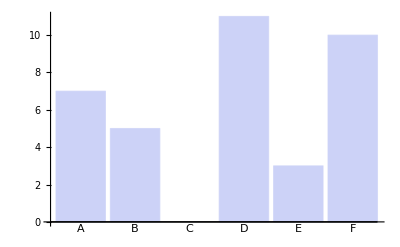

```mathematica
BarChart[("frequency"/.#)&/@loadedDieSpecification,ChartLabels->(("outcome"/.#)&/@loadedDieSpecification)]
```

```mathematica
testTally=Tally[nonUniformRandomSample[loadedDie,{100000}]]~Join~{{"C",0}}//SortBy[#,#⟦1⟧&]&
```

{{A,19508},{B,13921},{C,0},{D,30606},{E,8256},{F,27709}}

Formally checking the results would require a chi-squared test. Just go for "eyeballing" here:

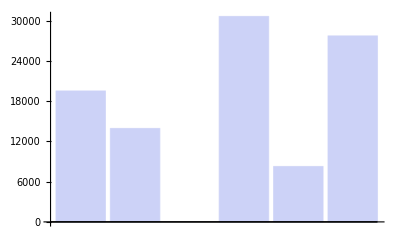

```mathematica
BarChart[#⟦2⟧&/@testTally,ChartLabels->#⟦1⟧&/@testTally]
```

#### Frequentized Random Instruction Strings

```mathematica
redistributedInstructions=redistributeFrequencies[frequentizedInstructions]
```

{{outcome→commI,foreignOutcome→ur,frequency→0,foreignFrequency→435},{outcome→conj2I,foreignOutcome→ul,frequency→0,foreignFrequency→435},{outcome→conjI,foreignOutcome→true,frequency→0,foreignFrequency→435},{outcome→div,foreignOutcome→Transpose,frequency→0,foreignFrequency→435},{outcome→inv,foreignOutcome→swap,frequency→0,foreignFrequency→435},{outcome→nop,foreignOutcome→ST,frequency→0,foreignFrequency→435},{outcome→det,foreignOutcome→plus,frequency→35,foreignFrequency→400},{outcome→tr,foreignOutcome→minus,frequency→35,foreignFrequency→400},{outcome→pop,foreignOutcome→lr,frequency→70,foreignFrequency→365},{outcome→rot,foreignOutcome→ll,frequency→70,foreignFrequency→365},{outcome→uminus,foreignOutcome→false,frequency→70,foreignFrequency→365},{outcome→ST,foreignOutcome→dup,frequency→265,foreignFrequency→170},{outcome→swap,foreignOutcome→dot,frequency→265,foreignFrequency→170},{outcome→Transpose,foreignOutcome→conj2,frequency→265,foreignFrequency→170},{outcome→true,foreignOutcome→conj,frequency→265,foreignFrequency→170},{outcome→ul,foreignOutcome→comm,frequency→265,foreignFrequency→170},{outcome→ur,foreignOutcome→CHF,frequency→265,foreignFrequency→170},{outcome→minus,foreignOutcome→dup,frequency→300,foreignFrequency→135},{outcome→plus,foreignOutcome→dot,frequency→300,foreignFrequency→135},{outcome→false,foreignOutcome→conj2,frequency→335,foreignFrequency→100},{outcome→ll,foreignOutcome→conj,frequency→335,foreignFrequency→100},{outcome→lr,foreignOutcome→comm,frequency→335,foreignFrequency→100},{outcome→dot,foreignOutcome→CHF,frequency→395,foreignFrequency→40},{outcome→dup,foreignOutcome→CHF,frequency→395,foreignFrequency→40},{outcome→comm,foreignOutcome→CHF,frequency→430,foreignFrequency→5},{outcome→conj,foreignOutcome→CHF,frequency→430,foreignFrequency→5},{outcome→conj2,foreignOutcome→CHF,frequency→430,foreignFrequency→5},{outcome→CHF,foreignOutcome→Null,frequency→435,foreignFrequency→0}}

```mathematica
nRedistributedInstructions=Length@redistributedInstructions
```

28

```mathematica
heightRedistributedInstructions=
("frequency"/.(First@redistributedInstructions))+
("foreignFrequency"/.(First@redistributedInstructions))
```

435

```mathematica
ClearAll[randomInstructionString];
randomInstructionString[n_:100]:=nonUniformRandomSample[
nRedistributedInstructions,
heightRedistributedInstructions,
redistributedInstructions,
{n}]
```

```mathematica
pretty[ms_]:=ms
```

### Monte-Carlo Search

```mathematica
caught={};lastgood=commonbad=Table[{falseMatrix},{4}];count=0;score=0;
bin[bool_]:=If[bool,1,0];maxscore=0;scorevec={0,0,0,0};
```

```mathematica
trial[]:=
With[{rc=2000,ln=100},
Block[{$RecursionLimit=rc},
With[{g=randomInstructionString[ln]},
With[{
tt=execAll[{p,q},g],
tf=execAll[{p,aq},g],
ft=execAll[{ap,q},g],
ff=execAll[{ap,aq},g]},
With[{result={tt,tf,ft,ff}},
If[Length@tt>0&&Length@tf>0&&Length@ft>0&&Length@ff>0,
score=0;
score+=(scorevec⟦1⟧=bin[falsey[tt⟦1⟧]]);
score+=(scorevec⟦2⟧=bin[truthy[tf⟦1⟧]]);
score+=(scorevec⟦3⟧=bin[truthy[ft⟦1⟧]]);
score+=(scorevec⟦4⟧=bin[truthy[ff⟦1⟧]]);
maxscore=Max[score,maxscore];
If[falsey[tt⟦1⟧]&&truthy[tf⟦1⟧]&&truthy[ft⟦1⟧]&&truthy[ff⟦1⟧],
AppendTo[caught,{g,result}]];
If[{#⟦1⟧}&/@result=!=commonbad,
pretty[lastgood=result],
pretty@lastgood]]]]]]]
```

```mathematica
Dynamic[
{count,score,scorevec,maxscore,caught}]
```

```mathematica
Dynamic[pretty@lastgood]
```

```mathematica
Manipulate[foo,Button["Gen",foo=trial[]]]
```

```mathematica
count=0;Do[count++;trial[],{10}]
```

Dot::dotsh: Tensors {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}} and {TagBox[( GridBox[{{ have incompatible shapes.

Dot::dotsh: Tensors {TagBox[( GridBox[{{ and {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}} have incompatible shapes.

Dot::dotsh: Tensors {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}} and {TagBox[( GridBox[{{ have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

### Genetic Search

```mathematica
ClearAll[
(* GLOBAL STATE *)
pool,generation,
(* TUNING PARAMETERS *)
generationSize,
geneLength,
mutationProbability,
maxRecombinationPoints,
(* FUNCTIONS & RULES *)
repool,fitness,symbolizer,run,bin,
scoreResult,swap,recombine,mutate];

generationSize=4*3;(* must be divisible by four *)
mutationProbability=0.10;
geneLength=40; (* can change! *)
maxRecombinationPoints=geneLength/10;

bin[bool_]:=If[bool,1,0];

repool[]:=pool=Table[randomString[geneLength],{generationSize}];
repool[];

symbolizer=Dispatch[{
iul->"iul",iur->"iur",
ill->"ill",ilr->"ilr",
plus->"+",minus->"-",dot->".",
true->"t",false->"f",
falseMatrix->"f",trueMatrix->"t",
Transpose->"T"}];
scoreResult[{tt_,tf_,ft_,ff_}]:=Module[{score=0,scorevec=ConstantArray[0,4]},
If[Length@tt>0,
score=0;
score+=(scorevec⟦1⟧=bin[falsey[tt⟦1⟧]]);
score+=(scorevec⟦2⟧=bin[truthy[tf⟦1⟧]]);
score+=(scorevec⟦3⟧=bin[truthy[ft⟦1⟧]]);
score+=(scorevec⟦4⟧=bin[truthy[ff⟦1⟧]]);
];
{"score"->score,"scorevec"->scorevec}];
fitness[gene_]:=fitness[gene]=
Module[{score=0,scorevec=ConstantArray[0,4]},
With[{
tt=(clear[];push[p];push[q];exec[gene]),
tf=(clear[];push[p];push[aq];exec[gene]),
ft=(clear[];push[ap];push[q];exec[gene]),
ff=(clear[];push[ap];push[aq];exec[gene])},
With[{result={tt,tf,ft,ff}},
{"gene"->gene/.symbolizer,"result"->result/.symbolizer,
"length"->Length@gene}
~Join~(scoreResult@result)]]];
mutate[survivor_]:=
If[RandomReal[]<mutationProbability,
With[{position=RandomInteger[{1,"length"/.survivor}]},
With[{oldInstruction=("gene"/.survivor)⟦position⟧},
With[{newInstructionSet=Complement[instructionSet,{oldInstruction}]},
With[{newInstruction=RandomChoice[newInstructionSet]},
Module[{oldGene=("gene"/.survivor)},
(*Print[{position,oldInstruction,newInstruction,oldGene}/.symbolizer];*)
(oldGene⟦position⟧=newInstruction);
(*Print[{oldGene}/.symbolizer];*)
{"gene"->oldGene,
"length"->"length"/.survivor}]]]]],
survivor];
swap[{g1_,g2_},n_]:=
{g1⟦;;n⟧~Join~g2⟦n+1;;⟧,g2⟦;;n⟧~Join~g1⟦n+1;;⟧};
recombine[survivor1_,survivor2_]:=
With[{l=Min["length"/.survivor1,"length"/.survivor2]},
With[{rPoints=RandomInteger[{1,l},RandomInteger[{0,maxRecombinationPoints}]]//Union},
Fold[swap,{"gene"/.survivor1,"gene"/.survivor2},rPoints]]];
run[]:=
Module[{recombined,mutated,winners},
generation=Sort[
fitness/@pool,
{f,s}↦("score"/.f)>("score"/.s)];
winners=generation⟦;;generationSize/2⟧;
mutated=mutate/@winners;
If[Not@Divisible[generationSize,4],Throw["bad generationSize"]];
(*recombined=MapThread[recombine,{
mutated⟦;;generationSize/4⟧,
mutated⟦1+generationSize/4⟧;;}]//Flatten[#,1]&;*)
mutated
];
```

```mathematica
<<"Jacquard.m"
```

```mathematica
repool[];run[]/.symbolizer//Length
```

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

## I caught a fish!

```mathematica
ClearAll[firstFish,fish,tt,tf,ft,ff];
fish={CHF,dot,iul,AMV,iul,plus,ill,iul,CY,ill,AMV};
clear[];tt=exec[{p,q}~Join~fish];
clear[];tf=exec[{p,aq}~Join~fish];
clear[];ft=exec[{ap,q}~Join~fish];
clear[];ff=exec[{ap,aq}~Join~fish];
Grid[MapThread[Map,{{pretty[{#}]&,falsey[#⟦1⟧]&,Length},Table[{tt,tf,ft,ff},{3}]}]]
```

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

Part::partd: Part specification tt ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification tf ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Grid[{tt}] | Grid[{tf}] | Grid[{ft}] | Grid[{ff}]
False | False | False | False
0 | 0 | 0 | 0

```mathematica
PRENAND[m1_,m2_]:=iul+AMV[iul,m1.CHF[m2]]
```

```mathematica
Grid[{M/@MapThread[PRENAND,{{p,p,ap,ap},{q,aq,q,aq}}]}]
```

(1+a x+b z | b w+a y | 0 | 0
c x+d z | 1+d w+c y | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
AMV[CY[iul+AMV[iul,p.CHF[q]],ill,iul],ill]//M
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1+a x+b z | b w+a y | 0 | 0
c x+d z | 1+d w+c y | 0 | 0)

## HORIZON

Don't look below this line.

```mathematica
saveMe={{{CHF,dot,plus,{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},pop,AMV,{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},plus,{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},true,CY,{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},AMV,{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},pop,{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{{0,0,0,0},{0,0,0,0},{1+a x+b z,b w+a y,0,0},{c x+d z,1+d w+c y,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}}}};
```

### Other Primitive Operators

```mathematica
u3d=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}});u4d=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}});iul=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Dynamic@combos[u3d,p]
```

```mathematica
Dynamic@combos[u4d,p]
```

```mathematica
Dynamic@combos[u4d,p]
```